## Unsupervised classification of Iris flowers

In the first part of the practical, you will find clusters in the Iris flowers dataset. The main aim is to check to what extent the three species defined by biologists (Setosa, Versicolor, Virginica) are supported by the unsupervised clustering obtained using four features (sepal length, sepal width, petal length and petal width).

## Task 1

To start with, you should import and manipulate the data following the steps shown in Chapter 4.2 for classification of Iris flowers.

Import the Iris flowers data from “https://archive.ics.uci.edu/ml/machine-learning-databases/iris/iris.data”

```mathematica
data = SemanticImport["https://archive.ics.uci.edu/ml/machine-learning-databases/iris/iris.data"];
```

```mathematica
Flatten[Position[data, {}]]
```

{}

```mathematica
data = Delete[data, Flatten[Position[data, {}]]];
```

```mathematica
Flatten[Position[data, {}]]
```

{}

Clean the data (the resulting list was called irisDataUCI)

Define a list in which examples in the dataset are organised by species (I will refer to it as bySpecies below).

```mathematica
species = DeleteDuplicates[data[[All, 5]]] // Normal;
```

```mathematica
bySpecies = Cases[data, {__,__,__,__,#}] &/@ species;
```

```mathematica
bySpecies[[1]] // Normal;
```

## Task 2

Use a scree plot to study how the clustering error described in lectures depends on clustering obtained with the KMC method as a function of the number of clusters k. Do the results indicate that the data is best partitioned for k=3? In other words, is the classification into three species supported by the KMC unsupervised clustering method?

```mathematica
errorKMC[data_,k_]:=Module[{data0=data,nc=k,clusters,centre},
clusters=FindClusters[data0,nc,Method->"KMeans"];
centre=Table[Mean[clusters[[i]]],{i,1,nc}];
Total[Flatten[Table[Table[(EuclideanDistance[clusters[[i,j]],centre[[i]]])^2,{j,1,Length[clusters[[i]]]}],{i,1,Length[centre]}]]]]
```

```mathematica
errorKMC[data, 3]
```

89.3868

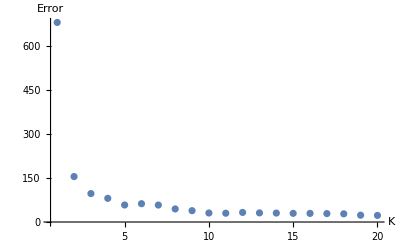

```mathematica
scree=Table[{k,errorKMC[data[[All, 1;;4]],k]},{k,1 , 20}];
ListPlot[scree,PlotRange->All,AxesLabel->{"K","Error"}]
```

```mathematica
2000/80
```

25

## Task 3

Use the ClusterClassify to define 3 classes for Iris flowers in an unsupervised way (use the KMC method). Calculate the purity of the unsupervised classification with respect to the true classes given in the dataset. For which species is the clustering “less pure”?

```mathematica
numbers = data[[All, 1;;4]] // Normal;
```

```mathematica
clusterings = FindClusters[numbers];
```

```mathematica
Length[clusterings];
```

```mathematica
NclusterVsRadius=Table[{r,
clusteringDBSCAN=FindClusters[numbers,Method->{"DBSCAN","NeighborhoodRadius"->r}];
Length[clusteringDBSCAN]},{r,0.1,2,0.1}];
```

```mathematica
NclusterVsRadius
```

{{0.1,147},{0.2,128},{0.3,84},{0.4,45},{0.5,9},{0.6,4},{0.7,2},{0.8,2},{0.9,2},{1.,2},{1.1,2},{1.2,2},{1.3,2},{1.4,2},{1.5,2},{1.6,1},{1.7,1},{1.8,1},{1.9,1},{2.,1}}

```mathematica
cc = ClusterClassify[numbers, 3, Method->"KMeans"]
```

ClassifierFunction[…]

```mathematica
bySpecies[[1]];
species1 = cc[bySpecies[[1]][[All, 1;;4]]]
```

{3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,1,3,3,3,3,3,3,3,3}

```mathematica
bySpecies[[2]];
```

```mathematica
species2 = cc[bySpecies[[2]][[All, 1;;4]]]
```

{2,2,2,1,2,1,2,1,2,1,1,1,1,1,1,2,1,1,1,1,2,1,1,1,1,2,2,2,1,1,1,1,1,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
Length[species2]
```

50

```mathematica
bySpecies[[3]];
```

```mathematica
species3 = cc[bySpecies[[3]][[All, 1;;4]]]
```

{2,1,2,2,2,2,1,2,2,2,2,2,2,1,2,2,2,2,2,1,2,1,2,2,2,2,2,2,2,2,2,2,2,2,1,2,2,2,2,2,2,2,1,2,2,2,1,2,2,2}

```mathematica
Count[species1,Commonest[species1][[1]]]
```

49

```mathematica
Count[species2,Commonest[species2][[1]]]
```

37

```mathematica
Count[species3,Commonest[species3][[1]]]
```

42

```mathematica
Purity[datain_,classifierin_,trueclassesin_]:=Module[{data=datain,classifier=classifierin,trueclasses=trueclassesin,Ncommonest},
Ncommonest=Table[Count[classifier[trueclasses[[i]]],Commonest[classifier[trueclasses[[i]]]][[1]]],{i,1,Length[trueclasses]}];
N[Total[Ncommonest]/Length[data]]
]
```

```mathematica
Purity[data,cc,Table[bySpecies[[i]][[All, 1;;4]], {i, 1, 3}]]
```

0.853333